```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11395];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
(*6->HV, SF1->25, SF2->26,U->27,D->28,U+D->,Monitor->30,TotN->32,Fill->31,RF->-1*)
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11395

```mathematica
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
Print["# Cycles = ",maxCy=data[[-1]][[2]]];
aCy=Round[(maxCy-4)/4];
mult=.000003902;
fita[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(-bb Cos[((xx-cc)*2Pi)/(180*mult)]),{{bb,.8},{cc,Mean[ftdata[[;;,1]]]}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]}}];
);
fitsa=Table[{{0,0},{0,0}},{k,1,aCy}];
pts=Table[{0,0},{k,1,4}];
aerr=Table[0,{k,1,maxCy-3}];
ptpts={};
For[i=1,i≤maxCy-4,i+=4,
For[j=0,j≤3,j++,
pts[[j+1]]={N[data[[i+j]][[-1]]/data[[i+j]][[-5]]],N[((data[[i+j]][[27]]-data[[i+j]][[28]])/(data[[i+j]][[27]]+data[[i+j]][[28]]))]};
aerr[[i+j]]=(Sqrt[data[[i+j]][[27]]]+Sqrt[data[[i+j]][[28]]])*Sqrt[2]/(data[[i+j]][[27]]+data[[i+j]][[28]]);
];
fitsa[[Round[((i-1)/4)+1]]]=fita[pts];
AppendTo[ptpts,pts];
];
```

# Cycles = 1047.

```mathematica
RootMeanSquare[fitsareal[[;;,1]][[;;,1]]]
```

0.683518

#Ramsey Clusters  = 261

Filtered #Ramsey Clusters  = 255

Alpha = 0.775261

Alpha Error = 0.0751742

A error = 0.0299142

bb x + cc : {{0.0000963817,0.0000380131},{0.762924,0.00561291}}

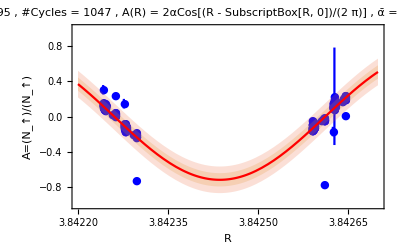

```mathematica
dispplot=Table[{Flatten[ptpts,1][[k]][[1]],{Flatten[ptpts,1][[k]][[2]],aerr[[k]]}},{k,1,aCy}];
fitsareal=Select[fitsa,(#[[1]][[1]]<.9&&#[[1]][[1]]>.5)&];
Print["#Ramsey Clusters  = ",Dimensions[fitsa][[1]]];
Print["Filtered #Ramsey Clusters  = ",dimfitsar=Dimensions[fitsareal][[1]]];
errptspt=Table[{k,{fitsareal[[;;,1]][[;;,1]][[k]],fitsareal[[;;,1]][[;;,2]][[k]]}},{k,1,dimfitsar}];
errptsptres=Table[N[fitsareal[[;;,1]][[;;,1]][[k]]-RootMeanSquare[fitsareal[[;;,1]][[;;,1]]]],{k,1,dimfitsar}];
Print["Alpha = ",Mean[fitsareal[[;;,1]][[;;,1]]]];
Print["Alpha Error = ",rmserra=RootMeanSquare[fitsareal[[;;,1]][[;;,2]]]];
Print["A error = ",RootMeanSquare[aerr]];
Print["bb x + cc : ",fitaln=fitln[Table[{k,fitsareal[[;;,1]][[;;,1]][[k]]},{k,1,dimfitsar}]]];
Show[{
EDAListPlot[dispplot,PlotStyle->{Blue},PlotMarkers->{Automatic,Medium},PlotRange->{{3.8422,3.8427},{-1,1}},Frame->True,FrameLabel->{"R","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},PlotLabel->"Run: 11395 , #Cycles = 1047 , A(R) = 2αCos[(R - SubscriptBox[R, 0])/(2  π)] , ᾱ = 0.77526 ± 0.07517",ImageSize->{1000}],Plot[{-fitsa[[1]][[1]][[1]] Cos[((xx-fitsa[[1]][[2]][[1]])*2Pi)/(180*mult)],
-fitsa[[1]][[1]][[1]] Cos[((xx-fitsa[[1]][[2]][[1]])*2Pi)/(180*mult)]+rmserra,
-fitsa[[1]][[1]][[1]] Cos[((xx-fitsa[[1]][[2]][[1]])*2Pi)/(180*mult)]-rmserra,
-fitsa[[1]][[1]][[1]] Cos[((xx-fitsa[[1]][[2]][[1]])*2Pi)/(180*mult)]+2rmserra,
-fitsa[[1]][[1]][[1]] Cos[((xx-fitsa[[1]][[2]][[1]])*2Pi)/(180*mult)]-2rmserra},{xx,3.8422,3.8427},PlotRange->{{3.8422,3.8427},{-1,1}},Frame->True,Filling->{{2->{3}},{4->{5}}},PlotStyle->{Red,None,None,None,None},PlotRange->Full,FrameLabel->{"R","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},PlotLabel->"Run: 11395, #Cycles = 1047 , A(R) = 2αCos[(R - SubscriptBox[R, 0])/(2  π)]  , ᾱ = 0.77526 ± 0.07517",ImageSize->{1000}]
}]
```

```mathematica
Plot[Sin[x],{x,0,10},Epilog->Inset[Graphics3D[Cylinder[],ImageSize->60,Boxed->False],{0.5,Center}]]
```

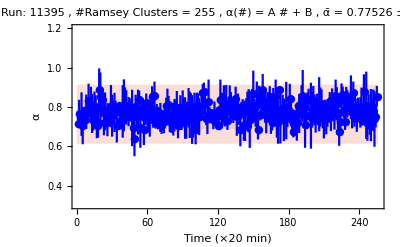

```mathematica
fitln[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(bb xx + cc),{{bb,0},{cc,Mean[fitsareal[[;;,1]][[;;,1]]]}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]}}];
);
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},Axes->False,PlotRange->{{-0.25,0.25},{0,50}},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{250}],Plot[4.5PDF[NormalDistribution[0,Sqrt[2]RootMeanSquare[aerr]],x],{x,-0.25,0.25},Axes->False,PlotRange->{{0.5,0.9},{0,50}}, Frame->True,Filling->Axis,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{0.5,0.9},{0,50}}, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}]
}];
Show[{
Plot[{0 xx + fitaln[[2]][[1]], fitaln[[2]][[1]]+RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]-RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]+2RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]-2RootMeanSquare[fitsareal[[;;,1]][[;;,2]]]},{xx,0,dimfitsar+1},Epilog->Inset[inset,{200,.45}],Filling->{{3->{2}},{4->{5}}},Axes->False,PlotRange->{{1,dimfitsar+1},{0.3,1.2}},Frame->True,FrameLabel->{"Time (×20 min)","α"},TicksStyle->Directive[FontSize->40],PlotStyle->{Red,None,None,None,None},LabelStyle->{18,Black},PlotLabel->"Run: 11395 , #Ramsey Clusters = 255 , α(#) = A # + B , ᾱ = 0.77526 ± 0.07517",ImageSize->{1000}],EDAListPlot[errptspt,PlotRange->{{1,dimfitsar+1},{0.3,1.2}},PlotMarkers->{Automatic,Medium},Frame->True,FrameLabel->{"Time (×20 min)","α"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},PlotStyle->Blue,PlotLabel->"Run: 11395 , #Ramsey Clusters = 255 , α(#) = A # + B , ᾱ = 0.77526 ± 0.07517",ImageSize->{1000}]}]
```

{{-0.0000978279,0.0000100661},{4.25936,0.683524},{0.772082,0.00288304}}

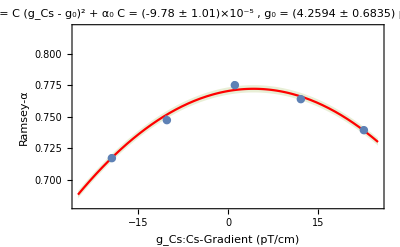

```mathematica
fitpar[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(bb(xx-cc)^2 +dd),{{bb,0},{cc,0},{dd,1}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]},{dd/.nlm[[1]][[2]],nlm["ParameterErrors"][[3]]}}];
);
gradpt={{1,{0.775,0.003}},{12,{0.764,0.003}},{-10.3,{0.748,0.003}},{22.5,{0.740,0.002}},{-19.5,{0.718,0.002}}};
fitgradpt=Table[{gradpt[[k]][[1]],gradpt[[k]][[2]][[1]]},{k,1,Dimensions[gradpt][[1]]}];
paradat=fitpar[fitgradpt]
Show[{
Plot[{paradat[[1]][[1]] (xx-paradat[[2]][[1]])^2 +paradat[[3]][[1]],paradat[[1]][[1]] (xx-paradat[[2]][[1]])^2+paradat[[3]][[1]]-paradat[[3]][[2]],paradat[[1]][[1]] (xx-paradat[[2]][[1]])^2+paradat[[3]][[1]]+paradat[[3]][[2]]},{xx,-25,25},Filling->{{3->{2}}},Axes->False,PlotRange->{{-25,25},{0.68,0.82}},Frame->True,FrameLabel->{"g_Cs:Cs-Gradient (pT/cm)","Ramsey-α"},TicksStyle->Directive[FontSize->40],PlotStyle->{Red,None,None},LabelStyle->{18,Black},PlotLabel->"α(g_z) = C g_z^2 + α_0 = C (g_Cs - g_0)^2 + α_0 \n C = (-9.78 ± 1.01)×10^-5 , g_0 = (4.2594 ± 0.6835) pT/cm , α_0 = (0.7720 ± 0.0029)",ImageSize->{1000}],
EDAListPlot[gradpt,PlotRange->{{-25,25},{0.68,0.82}},PlotMarkers->{Automatic,Medium},Frame->True,FrameLabel->{"g_Cs:Cs-Gradient (pT/cm)","Ramsey-α"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black,Bold},PlotLabel->"α(g_z) = C g_z^2 + α_0 = C (g_Cs - g_0)^2 + α_0 \n C = (-9.78 ± 1.01)×10^-5 , g_0 = (4.2594 ± 0.6835) pT/cm , α_0 = (0.7720 ± 0.0029)",ImageSize->{1000}]}]
```

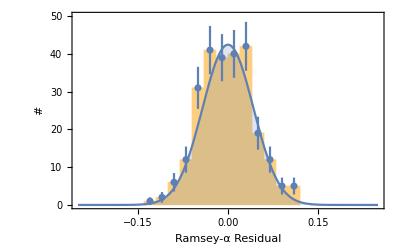

```mathematica
Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},Axes->False,PlotRange->{{-0.25,0.25},{0,50}},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{250}],Plot[4.5PDF[NormalDistribution[0,Sqrt[2]RootMeanSquare[aerr]],x],{x,-0.25,0.25},Axes->False,PlotRange->{{0.5,0.9},{0,50}}, Frame->True,Filling->Axis,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{0.5,0.9},{0,50}}, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}]
}]
```

```mathematica
HistogramList[errptsptres]
HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]]
```

{{-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25},{1,2,6,12,31,41,39,40,42,19,12,5,5}}

-1/50